# On the Stability and Motion of a Cube Balanced on a Cylinder

## Andre R. Guimaraes

Sam Houston State University - Physics Department

## Introduction to The Problem

A cube of side 2b and mass m is placed atop a fixed cylinder of radius R.
The cube is tilted by an angle θ.
There is only static friction, and no kinetic friction (the cube does no slip).

-Graphics-           -Graphics-

Note that the segment OverBar[B C_m] is the same length as path traveled by the cube on the cylinder (Rθ)

### Basic Equations

By looking at the diagram, it is easy to derive the equations for the position of the cube’s center of mass.

-Graphics-

x_Cm=(R+b)Sin(θ)-R θ Cos(θ)

y_Cm=(R+b)Cos(θ)+R θ Sin(θ)

## On the Stability of the Cube

Note that for a small interval of θ, the height of the center of mass of the cube rises slightly.

```mathematica
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);

posCM[θ_,r_,b_]:={(r+b)Sin[θ]-r θ Cos[θ],(r+b)Cos[θ]+r θ Sin[θ]}; 
(*Function to draw square section of cube*)
drawSquare[θ_,r_,b_]:={EdgeForm[{Thick,Blue}],FaceForm[],Rotate[Rectangle[posCM[θ,r,b]-{b,b},posCM[θ,r,b]+{b,b}],-θ]}
(*Initial Values for θ, r, and b*)
θ=0;
r=2;
b=1;
(*Function to numerically find critical angle*)
tcrit[r_,b_]:=t/.FindRoot[Tan[t]-r/b t==0,{t,1.5}]
(*Diagram of problem, manipulating θ, r, and b*)
Manipulate[
{
Show[
Graphics[{
drawSquare[θ,r,b],(*Section of Cube*)
Circle[{0,0},r],(*Secton of cylinder*)
Line[{{0,0},{r,0}}],(*Line of Cylinder's Radius*)
Line[{{0,0},{(r+b)Sin[θ],(r+b)Cos[θ]}}],(*Line form center of cylinder to center of mass of cube*)
Line[{posCM[θ,r,b],{(r+b)Sin[θ],(r+b)Cos[θ]}}],(*Line from center of cube to extension of radius, passing through the tangent point between cylinder and cube*)
Dashed,
InfiniteLine[{{0,0},{0,1}}],(*Vertical y-axis*)
InfiniteLine[{posCM[θ,r,b],posCM[θ,r,b]+{1,0}}],(*horizontal line going through cube's center of mass*)
Red,
InfiniteLine[{{0,0},{Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}],(*Line indicating positive critical angle*)
InfiniteLine[{{0,0},{-Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}](*Line indicating negative critical angle*)
}]
,PlotRange->{{-1.1(r+2b),1.1(r+2b)},{-1.1r,1.1(r+2b)}},ImageSize->Large]
,
Show[
Plot[posCM[θ,r,b][[2]],{θ,-π,π},PlotRange->{0,6},AxesLabel->{"θ","Height of C_m"},Ticks->{Range[-π,π,π/4],Range[1,6,1]}],
Graphics[{
Dashed,
InfiniteLine[{{θ,0},{θ,1}}],
Red,
InfiniteLine[{{tcrit[r,b],0},{tcrit[r,b],1}}],
InfiniteLine[{{-tcrit[r,b],0},{-tcrit[r,b],1}}]
}]
,ImageSize->Large]
}//Row
,{{θ,0},-π,π},{{r,2,"R"},0,10},{{b,1},0,10}]
AutoCollapse[]
```

### Finding Critical Angles

In order to find the critical angles for which the cube would topple out of the cylinder, we can simply find the first derivative of the potential energy (mgy_Cm) with respect to θ and equal it to zero.

mg(∂y_Cm)/(∂θ)=mg(b Sin(θ)-R θ Cos(θ))=0
b Sin(θ)=R θ Cos(θ)
Tan(θ)=R/b θ

Besides θ = 0, the roots of the equation cannot be found analytically.
We can, however, find approximate solutions by expanding Tan(θ) into a Taylor Series (Since -π/2≤θ≤π/2).

By Expanding to a third degree polynomial, we have Tan(θ)≈θ+θ^3/3, so:

θ+θ^3/3=R/b θ
θ(1-R/b)+θ^3/3=0
θ_Crit=±√(3(R/b-1))

### Finding Critical Angles

As a dummy example, we can assume R=2 and b=1. In this case, by comparing the approximate result found with the result found numerically, we find that the approximate result has a %Error of 48%.
The error will decrease with higher approximations and/or for smaller values of R/b.

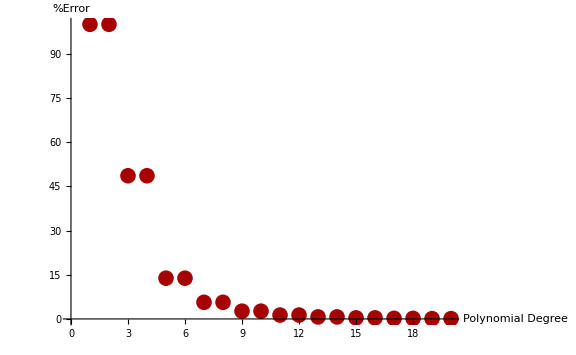

```mathematica
(*Exact value of critical angle for a given r and b*)
exactValue=t/.FindRoot[Tan[t]-r/b t==0,{t,1}];
(*List of approximate values for the calculation fo the critical angle depending on the degree of expansion of Tan[t] function*)
approxValue=t/.Table[FindRoot[Normal[Series[Tan[t],{t,0,n}]]-r/b t==0,{t,20}],{n,1,20}];

(*%Error of each approximation*)
percentErrors=Abs[approxValue-exactValue]/exactValue*100;
(*Plor of %Error of calculation of critical angle depending on the degree of approximation*)
ListPlot[percentErrors,AxesLabel->{"Polynomial Degree","%Error"},ImageSize->Large]
AutoCollapse[]
```

The approximations will always yield 2 non-trivial real solutions which are symmetrical along the y axis.

Except when b≥R, where the only solution for -π/2≤θ≤π/2is θ=0. Meaning there’s no stable regions.

### Different values for R/b

As R/b increases, the value for the critical θ_Crit decreases, such that, when R/b=1, the only solution is θ_Crit=0. If R/b>1, there are only complex, non-physical solutions.

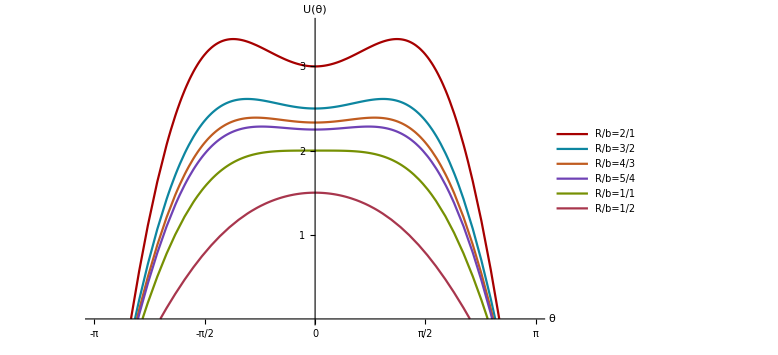

```mathematica
Plot[{posCM[θ,2,1][[2]],posCM[θ,3/2,1][[2]],posCM[θ,4/3,1][[2]],posCM[θ,5/4,1][[2]],posCM[θ,1,1][[2]],posCM[θ,.5,1][[2]]},{θ,-π,π},PlotRange->{0,3.5},AxesLabel->{"θ","U(θ)"},Ticks->{Range[-π,π,π/4],Range[1,6,1]},PlotLegends->LineLegend[{"R/b=2/1","R/b=3/2","R/b=4/3","R/b=5/4","R/b=1/1","R/b=1/2"}],ImageSize->Large]
AutoCollapse[]
```

### Different values for R/b

```mathematica
Manipulate[
{
Show[
Plot[posCM[θ,r,b][[2]],{θ,-Pi,Pi},PlotRange->{0,6},AxesLabel->{"θ","U(θ)"}]
,ImageSize->Large,Ticks->{Range[-π,π,π/4],Range[1,6,1]}],
Show[
Plot[Tan[θ]-r/b θ,{θ,-Pi,Pi},PlotRange->{-5,5},AxesLabel->{"θ","Tan(θ)-R/bθ"}]
,ImageSize->Large,Ticks->{Range[-π,π,π/4],Range[1,6,1]}]
}//Row
,{{r,2,"R"},0,3},{{b,1},0,3}]
AutoCollapse[]
```

Note that there are no real solutions for R/b>1, meaning the cube’s side must always be smaller then the cylinder’s diameter in order for any stability to happen.

### Special Situation

As a final thought we can examine the cases where θ cannot exceed an arc length greater then b (if it did the cube would start balancing on its edge). We can then impose that the situations where R θ_Crit≥b, is stable at all angles.
From this, we conclude:
R/b θ_Crit≥1
Tan(θ_Crit)≥1
θ_Crit≥π/4(For 0≤θ_Crit≤π/2 )
b≤π/4 R

In conclusion, is the side of the cube is 78% or less of the diameter of the cylinder, the system will be stable at all possible angles where the cube doesn’t balance on its edge.

## On the Motion of the Cube

### Assumptions

Given an initial angle θ_0<θ_Crit, and no initial velocity, the cube will rock back and forth, meaning the result will be of an oscillatory nature.

There is no friction affecting the motion of the cube.

### Lagrangian Approach

In order to solve the equation, we’ll need to use Lagrangian mechanics, meaning that the function ℒ=T-U, where T is the kinetic and U is the potential energy of the system, must satisfy the following condition.

∂/(∂t)((∂ℒ)/(∂θ̇))=(∂ℒ)/(∂θ)

### Lagrangian Approach

#### Kinetic Energy

T=(m v^2)/2+(I (θ̇)^2)/2

Where
v^2=(θ̇)^2(b^2+R^2 θ^2)
I=2/3 mb^2

So:
T=(m (θ̇)^2)/2(5/3 b^2+R^2 θ^2)

#### Potential Energy

U=m g((R+b)Cos(θ)+R θ Sin(θ))

#### Lagrangian

ℒ=(m (θ̇)^2)/2(5/3 b^2+R^2 θ^2)-m g((R+b)Cos(θ)+R θ Sin(θ))

### Lagrangian Approach

(∂ℒ)/(∂θ)=m (θ̇)^2 R^2 θ-mg(-b Sin(θ)+R θ Cos(θ))
(∂ℒ)/(∂θ̇)=m θ̇(5/3 b^2+R^2 θ^2)
∂/(∂t)((∂ℒ)/(∂θ̇))=m θ^(..)(5/3 b^2+R^2 θ^2)+2m (θ̇)^2 R^2 θ

After some algebraic manipulation, we get that the equation describing the motion of the cube is:

θ^(..)(5/3 b^2+R^2 θ^2)+(θ̇)^2 R^2 θ-g(b Sin(θ)-R θ Cos(θ))=0

Ugly and doesn’t have an analytical solution (at least, none that I could find)

Solvable by first order approximation.

Numerically solvable.

### First Order Approximation

Sin(θ)≈θ
Cos(θ)≈1
θ̇≈0
θ^2≈0

So:
5/3 b^2 θ^(..)=g θ(b-R)

By defining:
ω^2=(3g(R-b))/(5 b^2)     θ(0)=θ_0     θ̇(0)=ω_0.

We get:
θ^(..)+ω^2 θ=0

Which yields the solution:

θ(t)=θ_0 Cos(ω t)+ω_0/ω Sin(ω t)

### Comparison

By comparing the result obtained from the first order approximation, with the one found numerically for the real equation, we get:
(Parameters used: R = 2,b=1,g=9.81,θ_0=π/20,ω_0=0)

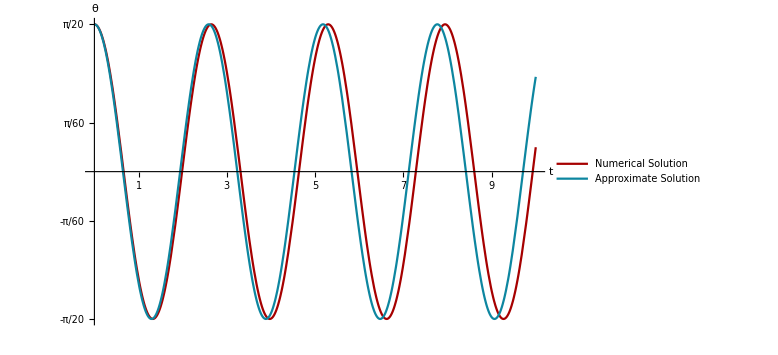

```mathematica
g=9.81;
θ0=π/20;
ω=√((3 g (r-b))/(5 b^2));
sol=NDSolve[{T''[t](5/3 b^2+r^2 T[t]^2)+T'[t]^2 r^2 T[t]==g(b Sin[T[t]]-r T[t]Cos[T[t]]),T[0]==θ0,T'[0]==0},T[t],{t,0,30}];
Plot[{T[t]/.sol,θ0 Cos[ω t]},{t,0,10},PlotLegends->LineLegend[{"Numerical Solution","Approximate Solution"}],ImageSize->Large,AxesLabel->{"t","θ"},Ticks->{Range[1,10,1],Range[-Pi/20,Pi/20,Pi/30]}]
AutoCollapse[]
```

### When θ_0>θ_Crit

Worthy noting that the angle increases in the beginning.

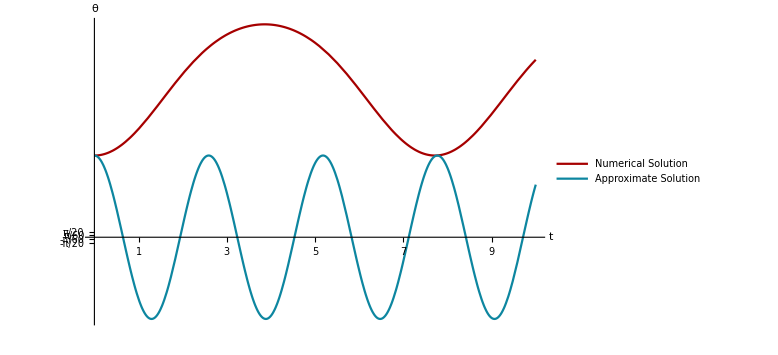

```mathematica
θ0=(3Pi)/4;
g=9.81;
ω=√((3 g (r-b))/(5 b^2));
sol=NDSolve[{T''[t](5/3 b^2+r^2 T[t]^2)+T'[t]^2 r^2 T[t]==g(b Sin[T[t]]-r T[t]Cos[T[t]]),T[0]==θ0,T'[0]==0},T[t],{t,0,30}];
Plot[{T[t]/.sol,θ0 Cos[ω t]},{t,0,10},PlotLegends->LineLegend[{"Numerical Solution","Approximate Solution"}],ImageSize->Large,AxesLabel->{"t","θ"},Ticks->{Range[1,10,1],Range[-Pi/20,Pi/20,Pi/30]}]
AutoCollapse[]
```

Periodicity probably due to geometry of the problem.

### Some Animations

```mathematica
g=9.81;
ω=√((3 g (r-b))/(5 b^2));
r=2;
b=1.7;
sol1=Evaluate[NDSolve[{T''[t](5/3 b^2+r^2 T[t]^2)+T'[t]^2 r^2 T[t]==g(b Sin[T[t]]-r T[t]Cos[T[t]]),T[0]==Pi/20,T'[0]==0},T,{t,0,30}]];
sol2=Evaluate[NDSolve[{T''[t](5/3 b^2+r^2 T[t]^2)+T'[t]^2 r^2 T[t]==g(b Sin[T[t]]-r T[t]Cos[T[t]]),T[0]==Pi/4,T'[0]==0},T,{t,0,30}]];
T1[t_]:=(T[t]/.sol1)[[1]];
T2[t_]:=(T[t]/.sol2)[[1]];
Animate[
{Show[
Graphics[{
drawSquare[T1[t],r,b],(*Section of Cube*)
Circle[{0,0},r],(*Secton of cylinder*)
Dashed,
InfiniteLine[{{0,0},{0,1}}],(*Vertical y-axis*)
Red,
InfiniteLine[{{0,0},{Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}],(*Line indicating positive critical angle*)
InfiniteLine[{{0,0},{-Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}](*Line indicating negative critical angle*)
}]
,PlotRange->{{-1.1(r+2b),1.1(r+2b)},{-1.1r,1.1(r+2b)}},ImageSize->450,PlotLabel->"Numerical Result with θ_0<θ_Crit"]
,
Show[
Graphics[{
drawSquare[T2[t],r,b],(*Section of Cube*)
Circle[{0,0},r],(*Secton of cylinder*)
Dashed,
InfiniteLine[{{0,0},{0,1}}],(*Vertical y-axis*)
Red,
InfiniteLine[{{0,0},{Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}],(*Line indicating positive critical angle*)
InfiniteLine[{{0,0},{-Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}](*Line indicating negative critical angle*)
}]
,PlotRange->{{-1.1(r+2b),1.1(r+2b)},{-1.1r,1.1(r+2b)}},ImageSize->450,PlotLabel->"Numerical Result with θ_0>θ_Crit"]
,
Show[
Graphics[{
drawSquare[Pi/20 Cos[ω t],r,b],(*Section of Cube*)
Circle[{0,0},r],(*Secton of cylinder*)
Dashed,
InfiniteLine[{{0,0},{0,1}}],(*Vertical y-axis*)
Red,
InfiniteLine[{{0,0},{Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}],(*Line indicating positive critical angle*)
InfiniteLine[{{0,0},{-Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}](*Line indicating negative critical angle*)
}]
,PlotRange->{{-1.1(r+2b),1.1(r+2b)},{-1.1r,1.1(r+2b)}},ImageSize->450,PlotLabel->"Approximate Result with θ_0<θ_Crit"]
,
Show[
Graphics[{
drawSquare[Pi/4 Cos[ω t],r,b],(*Section of Cube*)
Circle[{0,0},r],(*Secton of cylinder*)
Dashed,
InfiniteLine[{{0,0},{0,1}}],(*Vertical y-axis*)
Red,
InfiniteLine[{{0,0},{Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}],(*Line indicating positive critical angle*)
InfiniteLine[{{0,0},{-Sin[tcrit[r,b]],Cos[tcrit[r,b]]}}](*Line indicating negative critical angle*)
}]
,PlotRange->{{-1.1(r+2b),1.1(r+2b)},{-1.1r,1.1(r+2b)}},ImageSize->450,PlotLabel->"Approximate Result with θ_0>θ_Crit"]

}//Row
,{{t,0,"time"},0,10}]
AutoCollapse[]
```

## Conclusions

Many useful results can be drawn from the analysis of the stability of the cube, such as the critical angles for a given system, and the limits of the size of the cube for zero or total stability with respect to the cylinder.

As there is no simple analytical solution to be found for the differential equation describing the motion of the cube, the only way to foresee its behavior is through numerical calculations.

## References

A. Belendez, C. Pascual, D.I. Mendez, T. Belendez, and C. Neipp. Exact Solution for the Nonlinear Pendulum. Revista Brasileira de Ensino de Fisica, v. 29, n. 4, p. 645-648, (2007)

David Morin. Chapter 6: The Lagrangian Method. Draft Version.

# Thank You!

Mathematica Code: “https://github.com/andrerg01/mathematica-codes”